```mathematica
(*Mathematica*)
```

```mathematica
(* solve quadratic polynomials with discriminant  Negative Prime[n]*)
```

```mathematica
Clear[a,p]
```

```mathematica
Table[{Prime[n],a,x^2-a*x+1}/.NSolve[Discriminant[x^2-a*x+1,x]+Prime[n]==0,a],{n,PrimePi[41]}]
```

{{{2,-1.41421,1+1.41421 x+x^2},{2,1.41421,1-1.41421 x+x^2}},{{3,-1.,1+1. x+x^2},{3,1.,1-1. x+x^2}},{{5,0.-1. ⅈ,1+(0.+1. ⅈ) x+x^2},{5,0.+1. ⅈ,1-(0.+1. ⅈ) x+x^2}},{{7,0.-1.73205 ⅈ,1+(0.+1.73205 ⅈ) x+x^2},{7,0.+1.73205 ⅈ,1-(0.+1.73205 ⅈ) x+x^2}},{{11,0.-2.64575 ⅈ,1+(0.+2.64575 ⅈ) x+x^2},{11,0.+2.64575 ⅈ,1-(0.+2.64575 ⅈ) x+x^2}},{{13,0.-3. ⅈ,1+(0.+3. ⅈ) x+x^2},{13,0.+3. ⅈ,1-(0.+3. ⅈ) x+x^2}},{{17,0.-3.60555 ⅈ,1+(0.+3.60555 ⅈ) x+x^2},{17,0.+3.60555 ⅈ,1-(0.+3.60555 ⅈ) x+x^2}},{{19,0.-3.87298 ⅈ,1+(0.+3.87298 ⅈ) x+x^2},{19,0.+3.87298 ⅈ,1-(0.+3.87298 ⅈ) x+x^2}},{{23,0.-4.3589 ⅈ,1+(0.+4.3589 ⅈ) x+x^2},{23,0.+4.3589 ⅈ,1-(0.+4.3589 ⅈ) x+x^2}},{{29,0.-5. ⅈ,1+(0.+5. ⅈ) x+x^2},{29,0.+5. ⅈ,1-(0.+5. ⅈ) x+x^2}},{{31,0.-5.19615 ⅈ,1+(0.+5.19615 ⅈ) x+x^2},{31,0.+5.19615 ⅈ,1-(0.+5.19615 ⅈ) x+x^2}},{{37,0.-5.74456 ⅈ,1+(0.+5.74456 ⅈ) x+x^2},{37,0.+5.74456 ⅈ,1-(0.+5.74456 ⅈ) x+x^2}},{{41,0.-6.08276 ⅈ,1+(0.+6.08276 ⅈ) x+x^2},{41,0.+6.08276 ⅈ,1-(0.+6.08276 ⅈ) x+x^2}}}

```mathematica
p=Table[x^2-a*x+1/.NSolve[Discriminant[x^2-a*x+1,x]+Prime[n]==0,a][[1]],{n,PrimePi[43]}]
```

{1+1.41421 x+x^2,1+1. x+x^2,1+(0.+1. ⅈ) x+x^2,1+(0.+1.73205 ⅈ) x+x^2,1+(0.+2.64575 ⅈ) x+x^2,1+(0.+3. ⅈ) x+x^2,1+(0.+3.60555 ⅈ) x+x^2,1+(0.+3.87298 ⅈ) x+x^2,1+(0.+4.3589 ⅈ) x+x^2,1+(0.+5. ⅈ) x+x^2,1+(0.+5.19615 ⅈ) x+x^2,1+(0.+5.74456 ⅈ) x+x^2,1+(0.+6.08276 ⅈ) x+x^2,1+(0.+6.245 ⅈ) x+x^2}

```mathematica
lst=Table[x/.Solve[p[[i]]==0,x][[2]],{i,Length[p]}]
```

{-0.707107+0.707107 ⅈ,-0.5+0.866025 ⅈ,0.-1.61803 ⅈ,0.-2.1889 ⅈ,0.-2.98119 ⅈ,0.-3.30278 ⅈ,0.-3.86433 ⅈ,0.-4.11594 ⅈ,0.-4.57737 ⅈ,0.-5.19258 ⅈ,0.-5.38196 ⅈ,0.-5.91366 ⅈ,0.-6.24294 ⅈ,0.-6.40122 ⅈ}

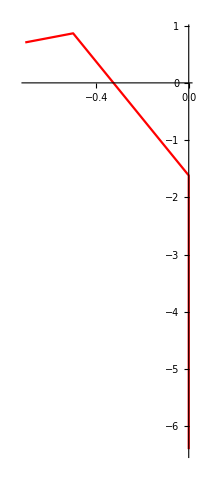

```mathematica
ComplexListPlot[lst,PlotRange->All,PlotStyle->Red,Joined->True]
```

```mathematica
(* solve quadratic polynomials with discriminant positive Prime[n]*)
```

```mathematica
Table[{Prime[n],a,x^2-a*x+1}/.NSolve[Discriminant[x^2-a*x+1,x]-Prime[n]==0,a],{n,PrimePi[43]}]
```

{{{2,-2.44949,1+2.44949 x+x^2},{2,2.44949,1-2.44949 x+x^2}},{{3,-2.64575,1+2.64575 x+x^2},{3,2.64575,1-2.64575 x+x^2}},{{5,-3.,1+3. x+x^2},{5,3.,1-3. x+x^2}},{{7,-3.31662,1+3.31662 x+x^2},{7,3.31662,1-3.31662 x+x^2}},{{11,-3.87298,1+3.87298 x+x^2},{11,3.87298,1-3.87298 x+x^2}},{{13,-4.12311,1+4.12311 x+x^2},{13,4.12311,1-4.12311 x+x^2}},{{17,-4.58258,1+4.58258 x+x^2},{17,4.58258,1-4.58258 x+x^2}},{{19,-4.79583,1+4.79583 x+x^2},{19,4.79583,1-4.79583 x+x^2}},{{23,-5.19615,1+5.19615 x+x^2},{23,5.19615,1-5.19615 x+x^2}},{{29,-5.74456,1+5.74456 x+x^2},{29,5.74456,1-5.74456 x+x^2}},{{31,-5.91608,1+5.91608 x+x^2},{31,5.91608,1-5.91608 x+x^2}},{{37,-6.40312,1+6.40312 x+x^2},{37,6.40312,1-6.40312 x+x^2}},{{41,-6.7082,1+6.7082 x+x^2},{41,6.7082,1-6.7082 x+x^2}},{{43,-6.85565,1+6.85565 x+x^2},{43,6.85565,1-6.85565 x+x^2}}}

```mathematica
p1=Table[x^2-a*x+1/.NSolve[Discriminant[x^2-a*x+1,x]-Prime[n]==0,a][[1]],{n,PrimePi[43]}]
```

{1+2.44949 x+x^2,1+2.64575 x+x^2,1+3. x+x^2,1+3.31662 x+x^2,1+3.87298 x+x^2,1+4.12311 x+x^2,1+4.58258 x+x^2,1+4.79583 x+x^2,1+5.19615 x+x^2,1+5.74456 x+x^2,1+5.91608 x+x^2,1+6.40312 x+x^2,1+6.7082 x+x^2,1+6.85565 x+x^2}

```mathematica
lst1=Table[x/.Solve[p1[[i]]==0,x],{i,Length[p]}]
```

{{-1.93185,-0.517638},{-2.1889,-0.45685},{-2.61803,-0.381966},{-2.98119,-0.335437},{-3.5948,-0.278179},{-3.86433,-0.258777},{-4.35284,-0.229735},{-4.57737,-0.218466},{-4.99599,-0.20016},{-5.56486,-0.179699},{-5.74192,-0.174158},{-6.24294,-0.160181},{-6.55566,-0.15254},{-6.70655,-0.149108}}

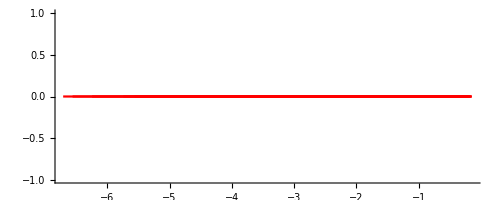

```mathematica
ComplexListPlot[lst1,PlotRange->All,PlotStyle->Red,Joined->True]
```

```mathematica
(* make quasrtic tetrahrdron polynomials (Gauss mapped)  as product of negative and positive discriminant quadratics*)
```

```mathematica
pp=Table[Expand[p[[i]]*p1[[i]]],{i,Length[p]}]
```

{1+3.8637 x+5.4641 x^2+3.8637 x^3+x^4,1+3.64575 x+4.64575 x^2+3.64575 x^3+x^4,1+(3.+1. ⅈ) x+(2.+3. ⅈ) x^2+(3.+1. ⅈ) x^3+x^4,1+(3.31662+1.73205 ⅈ) x+(2.+5.74456 ⅈ) x^2+(3.31662+1.73205 ⅈ) x^3+x^4,1+(3.87298+2.64575 ⅈ) x+(2.+10.247 ⅈ) x^2+(3.87298+2.64575 ⅈ) x^3+x^4,1+(4.12311+3. ⅈ) x+(2.+12.3693 ⅈ) x^2+(4.12311+3. ⅈ) x^3+x^4,1+(4.58258+3.60555 ⅈ) x+(2.+16.5227 ⅈ) x^2+(4.58258+3.60555 ⅈ) x^3+x^4,1+(4.79583+3.87298 ⅈ) x+(2.+18.5742 ⅈ) x^2+(4.79583+3.87298 ⅈ) x^3+x^4,1+(5.19615+4.3589 ⅈ) x+(2.+22.6495 ⅈ) x^2+(5.19615+4.3589 ⅈ) x^3+x^4,1+(5.74456+5. ⅈ) x+(2.+28.7228 ⅈ) x^2+(5.74456+5. ⅈ) x^3+x^4,1+(5.91608+5.19615 ⅈ) x+(2.+30.7409 ⅈ) x^2+(5.91608+5.19615 ⅈ) x^3+x^4,1+(6.40312+5.74456 ⅈ) x+(2.+36.7831 ⅈ) x^2+(6.40312+5.74456 ⅈ) x^3+x^4,1+(6.7082+6.08276 ⅈ) x+(2.+40.8044 ⅈ) x^2+(6.7082+6.08276 ⅈ) x^3+x^4,1+(6.85565+6.245 ⅈ) x+(2.+42.8135 ⅈ) x^2+(6.85565+6.245 ⅈ) x^3+x^4}

```mathematica
rts=Table[x/.NSolve[pp[[i]]==0,x],{i,Length[pp]}]
```

{{-1.93185,-0.707107-0.707107 ⅈ,-0.707107+0.707107 ⅈ,-0.517638},{-2.1889,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.45685},{-2.61803,-0.381966,0.+0.618034 ⅈ,0.-1.61803 ⅈ},{-2.98119,-0.335437,0.+0.45685 ⅈ,0.-2.1889 ⅈ},{-3.5948,-0.278179,0.+0.335437 ⅈ,0.-2.98119 ⅈ},{-3.86433,-0.258777,0.+0.302776 ⅈ,0.-3.30278 ⅈ},{-4.35284,-0.229735,0.+0.258777 ⅈ,0.-3.86433 ⅈ},{-4.57737,-0.218466,0.+0.242958 ⅈ,0.-4.11594 ⅈ},{-4.99599,-0.20016,0.+0.218466 ⅈ,0.-4.57737 ⅈ},{-5.56486,-0.179699,0.+0.192582 ⅈ,0.-5.19258 ⅈ},{-5.74192,-0.174158,0.+0.185806 ⅈ,0.-5.38196 ⅈ},{-6.24294,-0.160181,0.+0.1691 ⅈ,0.-5.91366 ⅈ},{-6.55566,-0.15254,0.+0.160181 ⅈ,0.-6.24294 ⅈ},{-6.70655,-0.149108,0.+0.15622 ⅈ,0.-6.40122 ⅈ}}

```mathematica
(*total discriminant quartic tetrahedron Polynomial*)
```

```mathematica
dis=Table[Discriminant[pp[[i]],x],{i,Length[pp]}]
```

{-4.59499,-66.0236,-700.+2400. ⅈ,3332.+9007.47 ⅈ,43076.+39676.2 ⅈ,92612.+66893.3 ⅈ,297092.+152802. ⅈ,475076.+214569. ⅈ,1.05165×10^6+383411. ⅈ,2.72148×10^6+772988. ⅈ,3.57108×10^6+945343. ⅈ,7.32141×10^6+1.6114×10^6 ⅈ,1.10879×10^7+2.19495×10^6 ⅈ,1.34385×10^7+2.53319×10^6 ⅈ}

```mathematica
Table[Discriminant[pp[[i]],x]/Prime[i]^2,{i,Length[pp]}]
```

{-1.14875,-7.33596,-28.+96. ⅈ,68.+183.826 ⅈ,356.+327.902 ⅈ,548.+395.818 ⅈ,1028.+528.727 ⅈ,1316.+594.374 ⅈ,1988.+724.784 ⅈ,3236.+919.13 ⅈ,3716.+983.707 ⅈ,5348.+1177.06 ⅈ,6596.+1305.74 ⅈ,7268.+1370.03 ⅈ}

```mathematica
Clear[a,x]
```

```mathematica
rtsn=Table[-x/.NSolve[pp[[i]]==0,x],{i,Length[pp]}]
```

{{1.93185,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.517638},{2.1889,0.5+0.866025 ⅈ,0.5-0.866025 ⅈ,0.45685},{2.61803,0.381966,0.-0.618034 ⅈ,0.+1.61803 ⅈ},{2.98119,0.335437,0.-0.45685 ⅈ,0.+2.1889 ⅈ},{3.5948,0.278179,0.-0.335437 ⅈ,0.+2.98119 ⅈ},{3.86433,0.258777,0.-0.302776 ⅈ,0.+3.30278 ⅈ},{4.35284,0.229735,0.-0.258777 ⅈ,0.+3.86433 ⅈ},{4.57737,0.218466,0.-0.242958 ⅈ,0.+4.11594 ⅈ},{4.99599,0.20016,0.-0.218466 ⅈ,0.+4.57737 ⅈ},{5.56486,0.179699,0.-0.192582 ⅈ,0.+5.19258 ⅈ},{5.74192,0.174158,0.-0.185806 ⅈ,0.+5.38196 ⅈ},{6.24294,0.160181,0.-0.1691 ⅈ,0.+5.91366 ⅈ},{6.55566,0.15254,0.-0.160181 ⅈ,0.+6.24294 ⅈ},{6.70655,0.149108,0.-0.15622 ⅈ,0.+6.40122 ⅈ}}

```mathematica
pp1=Table[ExpandAll[Product[x-rtsn[[i,j]],{j,4}]]//Chop,{i,Length[rtsn]}]
```

{1.-3.8637 x+5.4641 x^2-3.8637 x^3+x^4,1.-3.64575 x+4.64575 x^2-3.64575 x^3+x^4,1.-(3.+1. ⅈ) x+(2.+3. ⅈ) x^2-(3.+1. ⅈ) x^3+x^4,1.-(3.31662+1.73205 ⅈ) x+(2.+5.74456 ⅈ) x^2-(3.31662+1.73205 ⅈ) x^3+x^4,1.-(3.87298+2.64575 ⅈ) x+(2.+10.247 ⅈ) x^2-(3.87298+2.64575 ⅈ) x^3+x^4,1.-(4.12311+3. ⅈ) x+(2.+12.3693 ⅈ) x^2-(4.12311+3. ⅈ) x^3+x^4,1.-(4.58258+3.60555 ⅈ) x+(2.+16.5227 ⅈ) x^2-(4.58258+3.60555 ⅈ) x^3+x^4,1.-(4.79583+3.87298 ⅈ) x+(2.+18.5742 ⅈ) x^2-(4.79583+3.87298 ⅈ) x^3+x^4,1.-(5.19615+4.3589 ⅈ) x+(2.+22.6495 ⅈ) x^2-(5.19615+4.3589 ⅈ) x^3+x^4,1.-(5.74456+5. ⅈ) x+(2.+28.7228 ⅈ) x^2-(5.74456+5. ⅈ) x^3+x^4,1.-(5.91608+5.19615 ⅈ) x+(2.+30.7409 ⅈ) x^2-(5.91608+5.19615 ⅈ) x^3+x^4,1.-(6.40312+5.74456 ⅈ) x+(2.+36.7831 ⅈ) x^2-(6.40312+5.74456 ⅈ) x^3+x^4,1.-(6.7082+6.08276 ⅈ) x+(2.+40.8044 ⅈ) x^2-(6.7082+6.08276 ⅈ) x^3+x^4,1.-(6.85565+6.245 ⅈ) x+(2.+42.8135 ⅈ) x^2-(6.85565+6.245 ⅈ) x^3+x^4}

```mathematica
(* tetrahedral rectangles:cube analogs genrated with prime discrimants*)
```

```mathematica
pr=Table[Rationalize[Expand[pp[[i]]*pp1[[i]]]//Chop],{i,Length[pp]}]
```

{1-4 x^2+2 x^4-4 x^6+x^8,1-4 x^2-3 x^4-4 x^6+x^8,1-4 x^2-19 x^4-4 x^6+x^8,1-4 x^2-43 x^4-4 x^6+x^8,1-4 x^2-115 x^4-4 x^6+x^8,1-4 x^2-163 x^4-4 x^6+x^8,1-4 x^2-283 x^4-4 x^6+x^8,1-4 x^2-355 x^4-4 x^6+x^8,1-4 x^2-523 x^4-4 x^6+x^8,1-4 x^2-835 x^4-4 x^6+x^8,1-4 x^2-955 x^4-4 x^6+x^8,1-4 x^2-1363 x^4-4 x^6+x^8,1-4 x^2-1675 x^4-4 x^6+x^8,1-4 x^2-1843 x^4-4 x^6+x^8}

```mathematica
(* Pseudo-Cube Absolute Elliptical Invariants*)
```

```mathematica
Table[pr[[i]]^3/(108*z^4*(z^4-1)^4),{i,Length[pr]}]
```

{((1-4 x^2+2 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-3 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-19 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-43 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-115 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-163 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-283 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-355 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-523 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-835 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-955 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-1363 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-1675 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4),((1-4 x^2-1843 x^4-4 x^6+x^8)^3)/(108 z^4 (-1+z^4)^4)}

```mathematica
(*total discriminant Octic tetrahedal rectangle Polynomials*)
```

```mathematica
disr=Table[Discriminant[pr[[i]],x],{i,Length[pr]}]
```

{38654705664,1706597351424,1296000000000000,987834729227157504,2267622464117081702400,35742343143893088927744,2845720754159410057641984,17264791272937869346406400,377962482706045721460670464,15782064083384556980183040000,46098190007846151803176550400,789761962046837302605652230144,4099347047902914164057717145600,8798858376628388532150566191104}

```mathematica
pw=Table[Floor[N[Log[Discriminant[pr[[i]],x]]]],{i,Length[pr]}]
```

{24,28,34,41,49,51,56,58,61,64,66,68,70,71}

```mathematica
FindSequenceFunction[{24,28,34,41,49,51,56,58,61,64,66,68,70},x]
```

FindSequenceFunction[{24,28,34,41,49,51,56,58,61,64,66,68,70},x]

```mathematica
Table[N[Discriminant[pr[[i]],x]^(1/pw[[i]])]/Exp[1],{i,Length[pr]}]
```

{1.01587,1.00593,1.02375,1.01065,1.00354,1.01842,1.00551,1.00191,1.00323,1.01462,1.00001,1.01245,1.007,1.00356}

```mathematica
Table[N[Discriminant[pr[[i]],x]/Prime[i]^(pw[[i]])],{i,Length[pr]}]
```

{2304.,0.0745995,2.22651×10^-9,2.21648×10^-17,2.12485×10^-30,5.52169×10^-35,3.5404×10^-45,1.17342×10^-49,3.25125×10^-57,4.02431×10^-66,1.71322×10^-70,1.81878×10^-77,5.22209×10^-83,9.29321×10^-86}

```mathematica
Table[CoefficientList[pr[[i]],x][[5]],{i,Length[pr]}]
```

{2,-3,-19,-43,-115,-163,-283,-355,-523,-835,-955,-1363,-1675,-1843}

```mathematica
Abs[{2,-3,-19,-43,-115,-163,-283,-355,-523,-835,-955,-1363,-1675}]
```

{2,3,19,43,115,163,283,355,523,835,955,1363,1675}

```mathematica
FindSequenceFunction[{2,3,19,43,115,163,283,355,523,835,955,1363,1675},x]
```

FindSequenceFunction[{2,3,19,43,115,163,283,355,523,835,955,1363,1675},x]

```mathematica
(*hyperbolic tetrahedron  Absolute Elliptical Invariants*)
```

```mathematica
Table[pp[[i]]^3/pp1[[i]]^3,{i,Length[pp]}]
```

{((1+3.8637 x+5.4641 x^2+3.8637 x^3+x^4)^3)/((1.-3.8637 x+5.4641 x^2-3.8637 x^3+x^4)^3),((1+3.64575 x+4.64575 x^2+3.64575 x^3+x^4)^3)/((1.-3.64575 x+4.64575 x^2-3.64575 x^3+x^4)^3),((1+(3.+1. ⅈ) x+(2.+3. ⅈ) x^2+(3.+1. ⅈ) x^3+x^4)^3)/((1.-(3.+1. ⅈ) x+(2.+3. ⅈ) x^2-(3.+1. ⅈ) x^3+x^4)^3),((1+(3.31662+1.73205 ⅈ) x+(2.+5.74456 ⅈ) x^2+(3.31662+1.73205 ⅈ) x^3+x^4)^3)/((1.-(3.31662+1.73205 ⅈ) x+(2.+5.74456 ⅈ) x^2-(3.31662+1.73205 ⅈ) x^3+x^4)^3),((1+(3.87298+2.64575 ⅈ) x+(2.+10.247 ⅈ) x^2+(3.87298+2.64575 ⅈ) x^3+x^4)^3)/((1.-(3.87298+2.64575 ⅈ) x+(2.+10.247 ⅈ) x^2-(3.87298+2.64575 ⅈ) x^3+x^4)^3),((1+(4.12311+3. ⅈ) x+(2.+12.3693 ⅈ) x^2+(4.12311+3. ⅈ) x^3+x^4)^3)/((1.-(4.12311+3. ⅈ) x+(2.+12.3693 ⅈ) x^2-(4.12311+3. ⅈ) x^3+x^4)^3),((1+(4.58258+3.60555 ⅈ) x+(2.+16.5227 ⅈ) x^2+(4.58258+3.60555 ⅈ) x^3+x^4)^3)/((1.-(4.58258+3.60555 ⅈ) x+(2.+16.5227 ⅈ) x^2-(4.58258+3.60555 ⅈ) x^3+x^4)^3),((1+(4.79583+3.87298 ⅈ) x+(2.+18.5742 ⅈ) x^2+(4.79583+3.87298 ⅈ) x^3+x^4)^3)/((1.-(4.79583+3.87298 ⅈ) x+(2.+18.5742 ⅈ) x^2-(4.79583+3.87298 ⅈ) x^3+x^4)^3),((1+(5.19615+4.3589 ⅈ) x+(2.+22.6495 ⅈ) x^2+(5.19615+4.3589 ⅈ) x^3+x^4)^3)/((1.-(5.19615+4.3589 ⅈ) x+(2.+22.6495 ⅈ) x^2-(5.19615+4.3589 ⅈ) x^3+x^4)^3),((1+(5.74456+5. ⅈ) x+(2.+28.7228 ⅈ) x^2+(5.74456+5. ⅈ) x^3+x^4)^3)/((1.-(5.74456+5. ⅈ) x+(2.+28.7228 ⅈ) x^2-(5.74456+5. ⅈ) x^3+x^4)^3),((1+(5.91608+5.19615 ⅈ) x+(2.+30.7409 ⅈ) x^2+(5.91608+5.19615 ⅈ) x^3+x^4)^3)/((1.-(5.91608+5.19615 ⅈ) x+(2.+30.7409 ⅈ) x^2-(5.91608+5.19615 ⅈ) x^3+x^4)^3),((1+(6.40312+5.74456 ⅈ) x+(2.+36.7831 ⅈ) x^2+(6.40312+5.74456 ⅈ) x^3+x^4)^3)/((1.-(6.40312+5.74456 ⅈ) x+(2.+36.7831 ⅈ) x^2-(6.40312+5.74456 ⅈ) x^3+x^4)^3),((1+(6.7082+6.08276 ⅈ) x+(2.+40.8044 ⅈ) x^2+(6.7082+6.08276 ⅈ) x^3+x^4)^3)/((1.-(6.7082+6.08276 ⅈ) x+(2.+40.8044 ⅈ) x^2-(6.7082+6.08276 ⅈ) x^3+x^4)^3),((1+(6.85565+6.245 ⅈ) x+(2.+42.8135 ⅈ) x^2+(6.85565+6.245 ⅈ) x^3+x^4)^3)/((1.-(6.85565+6.245 ⅈ) x+(2.+42.8135 ⅈ) x^2-(6.85565+6.245 ⅈ) x^3+x^4)^3)}

```mathematica
(*Search:seq:2,3,19,43,115,163,283,355,523,835,955,1363,1675

Sorry,but the terms do not match anything in the table.*)
```

```mathematica
(*end*)
```

```mathematica
Clear[x,y,z,pa,a0,b0,pt,pt1]
```

```mathematica
pt={1+3.863703305156273 x+5.464101615137754 x^2+3.863703305156273 x^3+x^4,1+3.6457513110645907 x+4.645751311064591 x^2+3.6457513110645907 x^3+x^4,1+(3.+1. ⅈ) x+(2.+3. ⅈ) x^2+(3.+1. ⅈ) x^3+x^4,1+(3.3166247903554+1.7320508075688772 ⅈ) x+(2.+5.744562646538029 ⅈ) x^2+(3.3166247903554+1.7320508075688772 ⅈ) x^3+x^4,1+(3.872983346207417+2.6457513110645907 ⅈ) x+(2.+10.2469507659596 ⅈ) x^2+(3.872983346207417+2.6457513110645907 ⅈ) x^3+x^4,1+(4.123105625617661+3. ⅈ) x+(2.+12.36931687685298 ⅈ) x^2+(4.123105625617661+3. ⅈ) x^3+x^4,1+(4.58257569495584+3.605551275463989 ⅈ) x+(2.+16.522711641858304 ⅈ) x^2+(4.58257569495584+3.605551275463989 ⅈ) x^3+x^4,1+(4.795831523312719+3.872983346207417 ⅈ) x+(2.+18.57417562100671 ⅈ) x^2+(4.795831523312719+3.872983346207417 ⅈ) x^3+x^4,1+(5.196152422706632+4.358898943540674 ⅈ) x+(2.+22.649503305812253 ⅈ) x^2+(5.196152422706632+4.358898943540674 ⅈ) x^3+x^4,1+(5.744562646538029+5. ⅈ) x+(2.+28.722813232690143 ⅈ) x^2+(5.744562646538029+5. ⅈ) x^3+x^4,1+(5.916079783099616+5.196152422706632 ⅈ) x+(2.+30.740852297878796 ⅈ) x^2+(5.916079783099616+5.196152422706632 ⅈ) x^3+x^4,1+(6.4031242374328485+5.744562646538029 ⅈ) x+(2.+36.78314831549904 ⅈ) x^2+(6.4031242374328485+5.744562646538029 ⅈ) x^3+x^4,1+(6.708203932499369+6.082762530298219 ⅈ) x+(2.+40.80441152620633 ⅈ) x^2+(6.708203932499369+6.082762530298219 ⅈ) x^3+x^4}
```

{1+3.8637 x+5.4641 x^2+3.8637 x^3+x^4,1+3.64575 x+4.64575 x^2+3.64575 x^3+x^4,1+(3.+1. ⅈ) x+(2.+3. ⅈ) x^2+(3.+1. ⅈ) x^3+x^4,1+(3.31662+1.73205 ⅈ) x+(2.+5.74456 ⅈ) x^2+(3.31662+1.73205 ⅈ) x^3+x^4,1+(3.87298+2.64575 ⅈ) x+(2.+10.247 ⅈ) x^2+(3.87298+2.64575 ⅈ) x^3+x^4,1+(4.12311+3. ⅈ) x+(2.+12.3693 ⅈ) x^2+(4.12311+3. ⅈ) x^3+x^4,1+(4.58258+3.60555 ⅈ) x+(2.+16.5227 ⅈ) x^2+(4.58258+3.60555 ⅈ) x^3+x^4,1+(4.79583+3.87298 ⅈ) x+(2.+18.5742 ⅈ) x^2+(4.79583+3.87298 ⅈ) x^3+x^4,1+(5.19615+4.3589 ⅈ) x+(2.+22.6495 ⅈ) x^2+(5.19615+4.3589 ⅈ) x^3+x^4,1+(5.74456+5. ⅈ) x+(2.+28.7228 ⅈ) x^2+(5.74456+5. ⅈ) x^3+x^4,1+(5.91608+5.19615 ⅈ) x+(2.+30.7409 ⅈ) x^2+(5.91608+5.19615 ⅈ) x^3+x^4,1+(6.40312+5.74456 ⅈ) x+(2.+36.7831 ⅈ) x^2+(6.40312+5.74456 ⅈ) x^3+x^4,1+(6.7082+6.08276 ⅈ) x+(2.+40.8044 ⅈ) x^2+(6.7082+6.08276 ⅈ) x^3+x^4}

```mathematica
a0=Table[Graphics3D[GraphicsComplex[{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[pt[[i]]==0,x],Polygon[…]]],{i,Length[pt]}];
```

```mathematica
pt1={1.0000000000000007-3.8637033051562746 x+5.464101615137755 x^2-3.8637033051562732 x^3+x^4,0.9999999999999996-3.64575131106459 x+4.64575131106459 x^2-3.6457513110645907 x^3+x^4,1.0000000000000002-(3.0000000000000004+1.0000000000000004 ⅈ) x+(2.0000000000000004+3. ⅈ) x^2-(3.+1. ⅈ) x^3+x^4,0.9999999999999998-(3.3166247903554+1.7320508075688767 ⅈ) x+(1.9999999999999998+5.744562646538028 ⅈ) x^2-(3.3166247903554+1.7320508075688772 ⅈ) x^3+x^4,0.9999999999999999-(3.8729833462074175+2.6457513110645907 ⅈ) x+(2.+10.246950765959602 ⅈ) x^2-(3.872983346207417+2.645751311064591 ⅈ) x^3+x^4,1.-(4.1231056256176615+2.9999999999999996 ⅈ) x+(2.+12.369316876852983 ⅈ) x^2-(4.123105625617661+3. ⅈ) x^3+x^4,1.-(4.58257569495584+3.6055512754639896 ⅈ) x+(2.+16.522711641858304 ⅈ) x^2-(4.58257569495584+3.6055512754639896 ⅈ) x^3+x^4,1.-(4.795831523312719+3.872983346207417 ⅈ) x+(2.+18.57417562100671 ⅈ) x^2-(4.795831523312719+3.872983346207417 ⅈ) x^3+x^4,1.0000000000000002-(5.196152422706634+4.358898943540675 ⅈ) x+(2.+22.649503305812257 ⅈ) x^2-(5.196152422706633+4.358898943540674 ⅈ) x^3+x^4,0.9999999999999998-(5.744562646538028+4.999999999999999 ⅈ) x+(1.9999999999999998+28.722813232690143 ⅈ) x^2-(5.744562646538028+5. ⅈ) x^3+x^4,1.-(5.916079783099617+5.196152422706632 ⅈ) x+(2.+30.7408522978788 ⅈ) x^2-(5.916079783099616+5.196152422706632 ⅈ) x^3+x^4,1.0000000000000002-(6.403124237432849+5.7445626465380295 ⅈ) x+(2.0000000000000004+36.78314831549904 ⅈ) x^2-(6.4031242374328485+5.744562646538029 ⅈ) x^3+x^4,1.0000000000000002-(6.70820393249937+6.08276253029822 ⅈ) x+(2.+40.80441152620634 ⅈ) x^2-(6.708203932499369+6.08276253029822 ⅈ) x^3+x^4}
```

{1.-3.8637 x+5.4641 x^2-3.8637 x^3+x^4,1.-3.64575 x+4.64575 x^2-3.64575 x^3+x^4,1.-(3.+1. ⅈ) x+(2.+3. ⅈ) x^2-(3.+1. ⅈ) x^3+x^4,1.-(3.31662+1.73205 ⅈ) x+(2.+5.74456 ⅈ) x^2-(3.31662+1.73205 ⅈ) x^3+x^4,1.-(3.87298+2.64575 ⅈ) x+(2.+10.247 ⅈ) x^2-(3.87298+2.64575 ⅈ) x^3+x^4,1.-(4.12311+3. ⅈ) x+(2.+12.3693 ⅈ) x^2-(4.12311+3. ⅈ) x^3+x^4,1.-(4.58258+3.60555 ⅈ) x+(2.+16.5227 ⅈ) x^2-(4.58258+3.60555 ⅈ) x^3+x^4,1.-(4.79583+3.87298 ⅈ) x+(2.+18.5742 ⅈ) x^2-(4.79583+3.87298 ⅈ) x^3+x^4,1.-(5.19615+4.3589 ⅈ) x+(2.+22.6495 ⅈ) x^2-(5.19615+4.3589 ⅈ) x^3+x^4,1.-(5.74456+5. ⅈ) x+(2.+28.7228 ⅈ) x^2-(5.74456+5. ⅈ) x^3+x^4,1.-(5.91608+5.19615 ⅈ) x+(2.+30.7409 ⅈ) x^2-(5.91608+5.19615 ⅈ) x^3+x^4,1.-(6.40312+5.74456 ⅈ) x+(2.+36.7831 ⅈ) x^2-(6.40312+5.74456 ⅈ) x^3+x^4,1.-(6.7082+6.08276 ⅈ) x+(2.+40.8044 ⅈ) x^2-(6.7082+6.08276 ⅈ) x^3+x^4}

```mathematica
b0=Table[Graphics3D[GraphicsComplex[{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[pt1[[i]]==0,x],Polygon[…]]],{i,Length[pt1]}];
```

```mathematica
Table[Show[{a0[[i]],b0[[i]],a0[[i]],b0[[i]]},ViewPoint->{3,3,3},ImageSize->Full],{i,Length[a0]}];
```

```mathematica
pt2={1-4 x^2+2 x^4-4 x^6+x^8,1-4 x^2-3 x^4-4 x^6+x^8,1-4 x^2-19 x^4-4 x^6+x^8,1-4 x^2-43 x^4-4 x^6+x^8,1-4 x^2-115 x^4-4 x^6+x^8,1-4 x^2-163 x^4-4 x^6+x^8,1-4 x^2-283 x^4-4 x^6+x^8,1-4 x^2-355 x^4-4 x^6+x^8,1-4 x^2-523 x^4-4 x^6+x^8,1-4 x^2-835 x^4-4 x^6+x^8,1-4 x^2-955 x^4-4 x^6+x^8,1-4 x^2-1363 x^4-4 x^6+x^8,1-4 x^2-1675 x^4-4 x^6+x^8}
```

{1-4 x^2+2 x^4-4 x^6+x^8,1-4 x^2-3 x^4-4 x^6+x^8,1-4 x^2-19 x^4-4 x^6+x^8,1-4 x^2-43 x^4-4 x^6+x^8,1-4 x^2-115 x^4-4 x^6+x^8,1-4 x^2-163 x^4-4 x^6+x^8,1-4 x^2-283 x^4-4 x^6+x^8,1-4 x^2-355 x^4-4 x^6+x^8,1-4 x^2-523 x^4-4 x^6+x^8,1-4 x^2-835 x^4-4 x^6+x^8,1-4 x^2-955 x^4-4 x^6+x^8,1-4 x^2-1363 x^4-4 x^6+x^8,1-4 x^2-1675 x^4-4 x^6+x^8}

```mathematica
Length[pt2]
```

13

```mathematica
c0=Table[Graphics3D[GraphicsComplex[{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[pt2[[i]]==0,x],Polygon[…]]],{i,Length[pt2]}];
```

```mathematica
(*g=Flatten[ParallelTable[Join[Table[Show[{a0[[i]],b0[[i]],a0[[i]],b0[[i]]},ViewPoint->{2-j/2,2-k/2,l/2},ImageSize->{940,560}],{i,Length[a0]}],Flatten[Table[Show[{{a0[[i]],b0[[i]]},{a0[[i]],b0[[i]]},c0[[i]],c0[[i]]},ViewPoint->{2-j/2,2-k/2,l/2},ImageSize->{940,560},PlotStyle->Opacity[0.5]],{i,Length[a0]}]]],{l,-1,1},{j,-2,1},{k,-1,2}]];
Export["Pseudo_Cubes4.mp4",g]
*)
```

```mathematica
g1=Flatten[ParallelTable[Join[Table[Show[{a0[[i]],b0[[i]],a0[[i]],b0[[i]]},ViewPoint->{3-2*j,3-2*k,3+2*l},ImageSize->{940,560}],{l,0,1},{j,0,1},{k,0,1}],Flatten[Table[Show[{{a0[[i]],b0[[i]]},{a0[[i]],b0[[i]]},c0[[i]],c0[[i]]},ViewPoint->{3-2*j,3-2*k,3+2*l},ImageSize->{940,560},PlotStyle->Opacity[0.5]],{l,0,1},{j,0,1},{k,0,1}]]],{i,Length[a0]}]];
```

```mathematica
Export["Pseudo_Cubes14.mp4",g1]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

Pseudo_Cubes14.mp4

```mathematica
(*end*)
```